```mathematica
Primorial[n_] := Times @@ Prime[Range[PrimePi[n]]]
```

```mathematica
Tick[x_/;x<=1] := Undefined
Tick[n_] := Prime[PrimePi[n]]
```

```mathematica
InversePrimorialCorrespondent[x_/;x≤1, k_] := Prime[k]
InversePrimorialCorrespondent[x_,k_] :=InversePrimorialCorrespondent[x/Prime[k+1],k+1]
InversePrimorialCorrespondent[x_] := InversePrimorialCorrespondent[x,0]
```

```mathematica
GsubPi[x_]:=Times @@ (Prime[Range[PrimePi[x]]]-1)
```

```mathematica
OmegaAtkin[n_] := n/Log[Log[n]]
```

```mathematica
OmegaPna[n_] := Sum[GsubPi[Prime[i]],{i,1,PrimePi[InversePrimorialCorrespondent[n]]-1}] + 2*(GsubPi[InversePrimorialCorrespondent[n]]* n/(Primorial[InversePrimorialCorrespondent[n]]-1))-PrimePi[n]+PrimePi[InversePrimorialCorrespondent[n]]
```

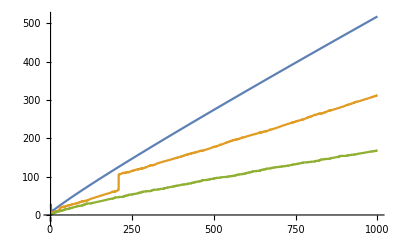

```mathematica
Plot[{OmegaAtkin[x], OmegaPna[x], PrimePi[x]},{x,2,1000}]
```

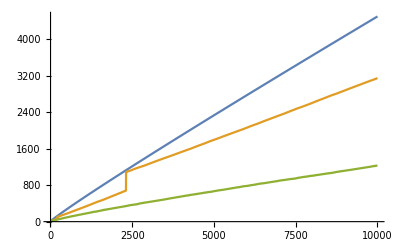

```mathematica
Plot[{OmegaAtkin[x], OmegaPna[x],PrimePi[x]},{x,2,10000}]
```

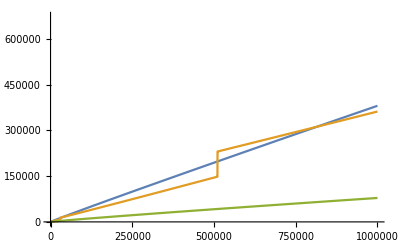

```mathematica
Plot[{OmegaAtkin[x], OmegaPna[x],PrimePi[x]},{x,2,1000000}]
```

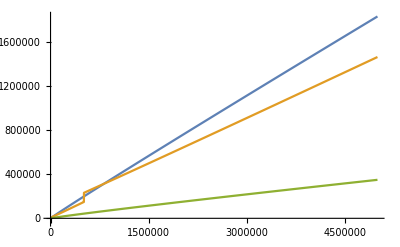

```mathematica
Plot[{OmegaAtkin[x], OmegaPna[x],PrimePi[x]},{x,2,5000000}]
```

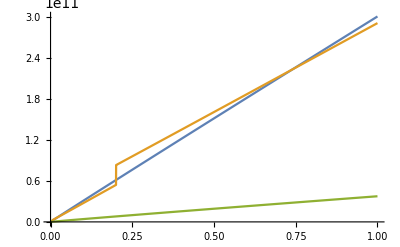

```mathematica
Plot[{OmegaAtkin[x], OmegaPna[x],PrimePi[x]},{x,2,1000000000000}]
```